```mathematica
Import[NotebookDirectory[]<>"WKB.m"];If[!IntegerQ[WKB`WKBFormulaOrder],Print["Old version of WKB.m - please update the file."]];
```

```mathematica
(* Dimensional Analysis*)
```

```mathematica
coeff1=4*Pi*(6.67*10^(-11))^3/(3^3*10^(24)*1.05*10^(-34));
coeff2=1.05*10^(-34)*(3*10^8)^3/(2*Pi*1.380649*10^(-23)*6.67*10^(-11));
```

```mathematica
(*可调数据：l（量子数）,M（黑洞质量）,q（无量纲荷质比）
相关函数：Q（黑洞电荷量），u（极端性），T（黑洞温度），c（量子修正强度），Φ（Dilaton），S（熵）*)
l=1;M=10^(1);q=0.9999;
Q=q*M*Sqrt[4*Pi*8.85*10^(-12)*6.67*10^(-11)];
u=Sqrt[1-q^2];
T=coeff2*u/(1-u)^2/M;
c=coeff1*(1+u)^3/(1-u)^2*M^3;
Φ=c*8*Pi*6.67*10^(-11);
cT=coeff1*coeff2*M^2*1.380649*10^(-23)/(3*10^8*1.05*10^(-34))*u*(1+u)/(1-u)^2
(*Entropy should be positive*)
S=4*Pi*M^2+4*Pi^2*Φ*(1.380649*10^(-23))^2*T/(1.05*10^(-34)*3*10^8)+3/2*Log[Φ*1.380649*10^(-23)*T/(1.05*10^(-34)*3*10^8)]
```

416817.

1245.82

```mathematica
(*从这里开始使用几何制，且设M=1*)
r1=1+u;
r2=1-u;
Tg=u/(2*Pi*r1^2);
β=1/Tg;
```

0.

0.

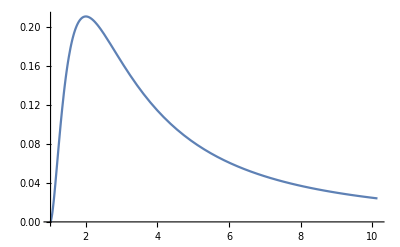

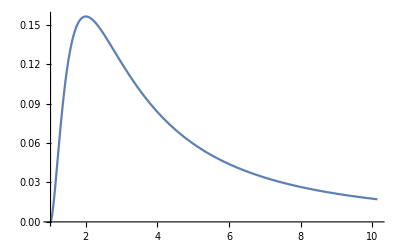

```mathematica
(*计算effective potential*)
f[r_]:=1-2/r+q^2/r^2;
Acor[r_]:=1+β/32/Pi^4/cT*
((r-r1)*(r-r2)*3/2*β^2*(Log[(r-r2)/(r-r1)])^2+
β^2*(6+(Log[(r-r2)/(r-r1)])^2)-6*Pi*β*(r-1)*Log[(r-r2)/(r-r1)]);

V[r_]:=1/r^2 f[r] ((l+l^2)*Acor[r]+2/r-2*q^2/r^2);
Vno[r_]:=1/r^2 f[r] ((l+l^2)+2/r-2*q^2/r^2);
DV[r_]:=D[V[r],r];
DVno[r_]:=D[Vno[r],r];
Limit[V[r],{r-> r1}]
Limit[V[r],{r-> ∞}]
Plot[V[r],{r,1*r1,10*r1}]
Plot[Vno[r],{r,r1,10*r1}]
```

```mathematica
(*修正后的QNMs*)
WKBQNM=WKBFormula[6,V[r],f[r],{r,2.},0]
```

{0.258443+4316.22 ⅈ,33.4007+33.3974 ⅈ,0.477682-0.082679 ⅈ,0.443331-0.0890854 ⅈ,0.4445-0.0947339 ⅈ,0.468384-0.0899033 ⅈ,r→2.00028}

```mathematica
(*修正前的QNMs*)
WKBQNMNo=WKBFormula[6,Vno[r],f[r],{r,2.3},0]
```

{2.62511-0.0884263 ⅈ,2.62511-0.0884263 ⅈ,2.62511-0.088426 ⅈ,2.6251-0.0884262 ⅈ,2.62511-0.0885936 ⅈ,2.6292-0.0884558 ⅈ,r→2.0004}

```mathematica
V[2.]
D[D[V[r],r],r]/.r->2
```

9.93403

-9.95915

```mathematica
{1780.1207947851096-1774.8663294511728 ⅈ,136.71633673660742-3.4351308250793022 ⅈ,21.757995479737097-21.584640140825904 ⅈ,2.7425277956116476-0.08821237098944044 ⅈ,2.625457492446936-0.09214579937071161 ⅈ,2.62532941862773-0.08842149064638542 ⅈ,2.625111251151356-0.08842883917055296 ⅈ,2.6251111655734545-0.08842629865618924 ⅈ,2.6251111831758687-0.08842629806325575 ⅈ,2.6251111714681596-0.08842595049585834 ⅈ,2.625104098370926-0.08842618875130362 ⅈ,2.625109743753773-0.08859362462528876 ⅈ,2.6292014064957647-0.08845575187344794 ⅈ,r->2.000398015807081}
```

```mathematica
N[Cos[Pi/8]]
```

0.92388

```mathematica
N[Sin[Pi/8]]
```

0.382683

```mathematica
0.92388/0.382683
```

2.41422

```mathematica
F[t,a]=(3(D[D[Tanh[rh*(t+a*e[t])/2],t],t])^2-2D[Tanh[rh*(t+a*e[t])/2],t]*(D[D[D[Tanh[rh*(t+a*e[t])/2],t],t],t]))/(D[Tanh[rh*(t+a*e[t])/2],t])^2
```

1/(rh^2 (1+a e'[t])^2)4 Cosh[1/2 rh (t+a e[t])]^4 (3 (-1/2 rh^2 Sech[1/2 rh (t+a e[t])]^2 Tanh[1/2 rh (t+a e[t])] (1+a e'[t])^2+1/2 a rh Sech[1/2 rh (t+a e[t])]^2 e''[t])^2-rh Sech[1/2 rh (t+a e[t])]^2 (1+a e'[t]) (-1/4 rh^3 Sech[1/2 rh (t+a e[t])]^4 (1+a e'[t])^3+1/2 rh^3 Sech[1/2 rh (t+a e[t])]^2 Tanh[1/2 rh (t+a e[t])]^2 (1+a e'[t])^3-3/2 a rh^2 Sech[1/2 rh (t+a e[t])]^2 Tanh[1/2 rh (t+a e[t])] (1+a e'[t]) e''[t]+1/2 a rh Sech[1/2 rh (t+a e[t])]^2 e^(3)[t]))

```mathematica
Series[F[t,a],{a,0,3}]//Simplify
```

rh^2+(2 rh^2 e'[t]-2 e^(3)[t]) a+(rh^2 e'[t]^2+3 e''[t]^2+2 e'[t] e^(3)[t]) a^2-2 (e'[t] (3 e''[t]^2+e'[t] e^(3)[t])) a^3+O[a]^4

```mathematica
FSe=Series[F[t,a],{a,0,3}]
```

rh^2 Sech[(rh t)/2]^2 (1+Sinh[(rh t)/2]^2)+(rh^3 e[t] Tanh[(rh t)/2]-rh^3 e[t] Sech[(rh t)/2]^2 Tanh[(rh t)/2]-rh^3 e[t] Tanh[(rh t)/2]^3+2 rh^2 Sech[(rh t)/2]^2 e'[t]+2 rh^2 Tanh[(rh t)/2]^2 e'[t]-2 e^(3)[t]) a+1/4 (rh^4 e[t]^2-rh^4 e[t]^2 Sech[(rh t)/2]^2-4 rh^4 e[t]^2 Tanh[(rh t)/2]^2+3 rh^4 e[t]^2 Sech[(rh t)/2]^2 Tanh[(rh t)/2]^2+3 rh^4 e[t]^2 Tanh[(rh t)/2]^4+8 rh^3 e[t] Tanh[(rh t)/2] e'[t]-8 rh^3 e[t] Sech[(rh t)/2]^2 Tanh[(rh t)/2] e'[t]-8 rh^3 e[t] Tanh[(rh t)/2]^3 e'[t]+4 rh^2 Sech[(rh t)/2]^2 e'[t]^2+4 rh^2 Tanh[(rh t)/2]^2 e'[t]^2+12 e''[t]^2+8 e'[t] e^(3)[t]) a^2+1/6 (-2 rh^5 e[t]^3 Tanh[(rh t)/2]+2 rh^5 e[t]^3 Sech[(rh t)/2]^2 Tanh[(rh t)/2]+5 rh^5 e[t]^3 Tanh[(rh t)/2]^3-3 rh^5 e[t]^3 Sech[(rh t)/2]^2 Tanh[(rh t)/2]^3-3 rh^5 e[t]^3 Tanh[(rh t)/2]^5+3 rh^4 e[t]^2 e'[t]-3 rh^4 e[t]^2 Sech[(rh t)/2]^2 e'[t]-12 rh^4 e[t]^2 Tanh[(rh t)/2]^2 e'[t]+9 rh^4 e[t]^2 Sech[(rh t)/2]^2 Tanh[(rh t)/2]^2 e'[t]+9 rh^4 e[t]^2 Tanh[(rh t)/2]^4 e'[t]+6 rh^3 e[t] Tanh[(rh t)/2] e'[t]^2-6 rh^3 e[t] Sech[(rh t)/2]^2 Tanh[(rh t)/2] e'[t]^2-6 rh^3 e[t] Tanh[(rh t)/2]^3 e'[t]^2-36 e'[t] e''[t]^2-12 e'[t]^2 e^(3)[t]) a^3+O[a]^4

```mathematica
Simplify[FSe]
```

rh^2+(2 rh^2 e'[t]-2 e^(3)[t]) a+(rh^2 e'[t]^2+3 e''[t]^2+2 e'[t] e^(3)[t]) a^2-2 (e'[t] (3 e''[t]^2+e'[t] e^(3)[t])) a^3+O[a]^4